# Figure 3

Data are imported from julia code https://github.com/djuliannader/RabiModel
Fixed ramp duration T_r=200

#### DataGS

```mathematica
DatPurR50={{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.994775725143428},{0.7,0.9936006656401877},{0.75,0.9921537418880904},{0.8,0.9903210142961318},{0.85,0.9879003610322292},{0.9,0.9844922503337201},{0.95,0.9791771590785479},{1,0.9693224813794615},{1.02,0.9624749424993903},{1.025,0.9603014280895678},{1.05,0.9450674965437998},{1.075,0.9184515579592468},{1.1,0.8785402990262056},{1.125,0.8367710422842245},{1.15,0.8026871790347999},{1.175,0.7750621854308065},{1.2,0.7514555074649951},{1.25,0.7121302675708026},{1.3,0.6805020299580149},{1.35,0.6546746928544679},{1.4,0.6333677520262117},{1.45,0.6156417139444618},{1.5,0.600786672980406}};
DatImpR50=Table[{DatPurR50[[i,1]],1-DatPurR50[[i,2]]},{i,1,Length[DatPurR50]}];
WminR50={{0.5,-6.454999001859804*10^-23},{0.55,-3.152359771837854*10^-25},{0.6,-1.2329517138702438*10^-20},{0.65,-1.459334120860238*10^-19},{0.7,-3.3077623636352352*10^-18},{0.75,-2.188476684149174*10^-14},{0.8,-3.424787019022922*10^-11},{0.85,-1.1537825015657825*10^-8},{0.9,-1.3478629241395159*10^-6},{0.95,6.97674252815073*10^-5},{1,-0.0016426570211678904},{1.02,0.004707557820296915},{1.05,0.020760077966225914},{1.075,0.052805795139885564},{1.1,0.10948300080287628},{1.125,0.15078997194560403},{1.15,0.17424608531386365},{1.175,0.18161190409818653},{1.2,0.18096115130831303},{1.25,0.1756882518602924},{1.3,0.1697735481844055},{1.35,0.1575490792228704},{1.4,0.14515006569266448},{1.45,0.13484341978668904},{1.5,0.12700297689027895}};
DestSqueezingR50={{0.5,0.43377926213546114},{0.55,0.41932933354269675},{0.6,0.40299496242170246},{0.65,0.38458029479914024},{0.7,0.3638308320435258},{0.75,0.34041670867905305},{0.8,0.3139041389962063},{0.85,0.2837091704766332},{0.9,0.24525449793127235},{0.95,0.20887744606648623},{1,0.16218859922700601},{1.02,0.1416912750852102},{1.05,0.1098790407453907},{1.075,0.08447774155460623},{1.1,0.0636307260148206},{1.125,0.049496206110248665},{1.15,0.04068162537227499},{1.175,0.03492594617873248},{1.2,0.03087094806117826},{1.25,0.025470433832121036},{1.3,0.0219948393387326},{1.35,0.01955164445956177},{1.4,0.017731219191109048},{1.45,0.016316608385585032},{1.5,0.015181589851748221}};
VarXR50={{0.5,0.43601934856889263},{0.55,0.42142699972321324},{0.6,0.4048873432490359},{0.65,0.3861758636775708},{0.7,0.3649994207827738},{0.75,0.3409673527282377},{0.8,0.3135465315785714},{0.85,0.2819921465130846},{0.9,0.24904165638103298},{0.95,0.20196423742664527},{1,0.15151462997586548},{1.02,0.1306476419149882},{1.05,0.10625739154523034},{1.075,0.11060981360438878},{1.1,0.1606983134889603},{1.125,0.2339414855306041},{1.15,0.2882501505072302},{1.175,0.3214015950610954},{1.2,0.34348850943781434},{1.25,0.37405033230931495},{1.3,0.3960145636908264},{1.35,0.4128694332860603},{1.4,0.4261691290662809},{1.45,0.436864189309941},{1.5,0.4455908649863728}};
DatSQratioR50=Table[{DestSqueezingR50[[i,1]],DestSqueezingR50[[i,2]]/VarXR50[[i,2]]},{i,1,Length[DestSqueezingR50]}];
DatCFIdispR50={{0.5,0.9234637453092736},{0.55,0.9180932516134328},{0.6,0.9163826928107061},{0.65,0.919793909566884},{0.7,0.930360454213807},{0.75,0.9511353101103044},{0.8,0.9870987723853518},{0.85,1.047186239559963},{0.9,1.1494342310196828},{0.95,1.336477904275941},{1,1.7342461789436114},{1.02,2.0326612795146364},{1.05,2.833582014918486},{1.075,4.121875890111434},{1.1,6.131761792440109},{1.125,8.278508646370144},{1.15,10.00786650190666},{1.175,11.361505989321829},{1.2,12.471579862666838},{1.25,14.191007144748756},{1.3,15.393130231496201},{1.35,16.180071126222305},{1.4,16.62623279783496},{1.45,16.79138681765701},{1.5,16.72502641543129}};
```

#### Datak0

```mathematica
(*Data obtained with ramp period Subscript[T, r]=200*)
DatPurR50k0={{0.5,0.9967489661007606},{0.55,0.9967945907721347},{0.60,0.9961687344238258},{0.65,0.9940795851861526},{0.70,0.9932433795384905},{0.75,0.9927065996969664},{0.80,0.9912770529529517},{0.85,0.9889307139879322},{0.90,0.9856473579206227},{0.95,0.9801795034186813},{1,0.9686550676894328},{1.02,0.9632139757944673},{1.05,0.9446617781277687},{1.075,0.9164817740252764},{1.10,0.8767890455354442},{1.125,0.8354770180343928},{1.135,0.8214627657694407},{1.15,0.8029419919492123},{1.175,0.7767378144284927},{1.2,0.7462144781217298},{1.25,0.707254353799547},{1.3,0.6748885224496087},{1.35,0.6462683162100489},{1.4,0.6298379035969538},{1.45,0.6236752340465409},{1.5,0.5993011452411218}};
DatImpR50k0=Table[{DatPurR50k0[[i,1]],1-DatPurR50k0[[i,2]]},{i,1,Length[DatPurR50k0]}];
WminR50k0={{0.5,2.4365952491770564*10^-9},{0.55,1.4479608682492588*10^-9},{0.60,9.089796038326196*10^-10},{0.65,4.669958495807006*10^-10},{0.70,5.1686198729970085*10^-9},{0.75,1.0586401602836983*10^-7},{0.80,8.233100386579557*10^-7},{0.85,4.42190190000585*10^-6},{0.90,2.392087434437206*10^-5},{0.95,0.00015118740102613957},{1,0.0015971340176013497},{1.02,0.005142018985458126},{1.05,0.021426906339937293},{1.075,0.05733868456349356},{1.10,0.11158623265767448},{1.125,0.15624335465012246},{1.135,0.16517011490443337},{1.15,0.17448273943313122},{1.175,0.18097068503425848},{1.2,0.18323528854487423},{1.25,0.17725316456007667},{1.3,0.1678674859511628},{1.35,0.1572887948727661},{1.4,0.1489641277683003},{1.45,0.1464686747627786},{1.5,0.13299291824843448}};
DestSqueezingR50k0={{0.5,0.4340876812813521},{0.55,0.4191938426046589},{0.60,0.40277842561846483},{0.65,0.38486767453813214},{0.70,0.36394393521785595},{0.75,0.34021818481185345},{0.80,0.31362284642072163},{0.85,0.2834458361477395},{0.90,0.24877748164460664},{0.95,0.20861518914383506},{1,0.16192350617365792},{1.02,0.1412270333114629},{1.05,0.10921429240298115},{1.075,0.0837045299449141},{1.10,0.06311796396693399},{1.125,0.04887114204358756},{1.135,0.045410914841193334},{1.15,0.04086138755694033},{1.175,0.03541316537356917},{1.2,0.0297092508962128},{1.25,0.024629830074379213},{1.3,0.021111295162272163},{1.35,0.018281084094482924},{1.4,0.017196619704437227},{1.45,0.017683735656434742},{1.5,0.01498914559711153}};
VarXR50k0={{0.5,0.436461250863967},{0.55,0.4212214124012281},{0.60,0.4045305984657671},{0.65,0.3867091931991857},{0.70,0.3652456027350275},{0.75,0.34055671541759536},{0.80,0.31289764591776253},{0.85,0.28134228355907326},{0.90,0.244584218139718},{0.95,0.20138642101537438},{1,0.151356348951917},{1.02,0.13005138262952015},{1.05,0.10600782238211089},{1.075,0.11174777623468429},{1.10,0.1633457046452613},{1.125,0.23961626415451612},{1.135,0.2591401030836237},{1.15,0.2863901004100357},{1.175,0.3175709738896345},{1.2,0.3553418740879591},{1.25,0.38289284084235375},{1.3,0.4105006306077283},{1.35,0.4255031985804816},{1.4,0.4512126744372763},{1.45,0.4708210889925819},{1.5,0.5114964885442825}};
DatSQratioR50k0=Table[{DestSqueezingR50k0[[i,1]],DestSqueezingR50k0[[i,2]]/VarXR50k0[[i,2]]},{i,1,Length[DestSqueezingR50k0]}];
DatCFIdispR50k0={{0.5,0.8905289160446952},{0.55,0.932769927052825},{0.60,0.9413223381854712},{0.65,0.8842650463467571},{0.70,0.9133290676696744},{0.75,0.9766034708324981},{0.80,1.0280826269980916},{0.85,1.087716444692212},{0.90,1.1914117225087606},{0.95,1.3707744984076813},{1,1.7215495534346992},{1.02,2.066466415027986},{1.05,2.8615662096327763},{1.075,4.162337704008185},{1.10,6.192692523010895},{1.125,8.416969366813131},{1.135,9.030686716141716},{1.15,9.959281752579907},{1.175,11.21726061377626},{1.2,12.898064987938548},{1.25,14.61933265461669},{1.3,15.920758543346453},{1.35,17.00168892947758},{1.4,16.966812904450286},{1.45,16.03669959464932},{1.5,16.85393628012666}};
```

#### Datak0.001

```mathematica
DatPurR50k1={{0.5,0.9965552390123155},{0.55,0.9957509604423759},{0.60,0.994925510530977},{0.65,0.9927081957741409},{0.70,0.9906632295201063},{0.75,0.9885904138049265},{0.80,0.9854917094791458},{0.85,0.9807952426830463},{0.90,0.9736940428210308},{0.95,0.9619745151789646},{1,0.9399707361917411},{1.025,0.9224989658144814},{1.05,0.8919583883255762},{1.075,0.841245188726661},{1.1,0.7708383128214628},{1.125,0.6991304813675118},{1.135,0.675394415667524},{1.15,0.6448161711511113},{1.175,0.6040735195853625},{1.20,0.5720436645434841},{1.25,0.5350495440875722},{1.30,0.5156719863027021},{1.35,0.5057641575405216},{1.40,0.5010498569535773},{1.45,0.498683743969564},{1.50,0.4971497970329319}};
DatImpR50k1=Table[{DatPurR50k1[[i,1]],1-DatPurR50k1[[i,2]]},{i,1,Length[DatPurR50k1]}];
WminR50k1={{0.5,4.6148133553708665*10^-11},{0.55,2.394745554784828*10^-12},{0.60,1.4032295616118812*10^-11},{0.65,7.120943913209033*10^-13},{0.70,4.3403973456378987*10^-13},{0.75,2.741124715542047*10^-13},{0.80,1.6027222146187698*10^-13},{0.85,6.439975467885116*10^-7},{0.90,7.378347690704539*10^-6},{0.95,7.171012964128455*10^-5},{1,0.001205156555451176},{1.025,0.005320002824870915},{1.05,0.017790591070231242},{1.075,0.04816634712407421},{1.1,0.09105684540160204},{1.125,0.1195920168115732},{1.135,0.1217428418797219},{1.15,0.1212756258085501},{1.175,0.11294152941041892},{1.20,0.10230286313739953},{1.25,0.07711751925703092},{1.30,0.05618207597204816},{1.35,0.04003490471393005},{1.4,0.02862193469927878},{1.45,0.020891657865486916},{1.5,0.013810593564654874}};
DestSqueezingR50k1={{0.5,0.43412076288236146},{0.55,0.41967615098935696},{0.60,0.4032958268091975},{0.65,0.38539197889483306},{0.70,0.3648985992471993},{0.75,0.34161842386270685},{0.80,0.31541055454758743},{0.85,0.2856947141516946},{0.90,0.25162001275105117},{0.95,0.21212630837041635},{1,0.16600779250492598},{1.025,0.14025962913425732},{1.05,0.11364057086167817},{1.075,0.08827182892708346},{1.1,0.06822050892944603},{1.125,0.05508189383097136},{1.135,0.0523353614716732},{1.15,0.048958992813355695},{1.175,0.04553879586454274},{1.20,0.041555426018066915},{1.25,0.04146778265880813},{1.30,0.04409167882347747},{1.35,0.04828389788944971},{1.4,0.05854722453161486},{1.45,0.05854722453161486},{1.5,0.08951249814416322}};
VarXR50k1={{0.5,0.4364132147859326},{0.55,0.42178950141391525},{0.60,0.40508326733861744},{0.65,0.3871259057371351},{0.70,0.36625653669373803},{0.75,0.34219663657270305},{0.80,0.3149901279735512},{0.85,0.2839589180219302},{0.90,0.2480033450063526},{0.95,0.20590268221234959},{1,0.15729229806598852},{1.025,0.13241340025547188},{1.05,0.11522997850108124},{1.075,0.12348294095986054},{1.1,0.17587493510621072},{1.125,0.24859727284496352},{1.135,0.2671976068455111},{1.15,0.29269446163005564},{1.175,0.3216604727758013},{1.20,0.35755854009085325},{1.25,0.3853904842202944},{1.30,0.412832610150521},{1.35,0.4288535711195904},{1.4,0.45432768413731794},{1.45,0.4722005703025467},{1.5,0.5079874180394898}};
DatSQratioR50k1=Table[{DestSqueezingR50k1[[i,1]],DestSqueezingR50k1[[i,2]]/VarXR50k1[[i,2]]},{i,1,Length[DestSqueezingR50k1]}];
DatCFIdispR50k1={{0.5,0.8789838155067915},{0.55,0.8705539650253474},{0.60,0.8723519533336521},{0.65,0.8225779520902736},{0.7,0.8071635598632738},{0.75,0.8160070886387317},{0.80,0.8235676099129378},{0.85,0.834635806115292},{0.90,0.8648893844654385},{0.95,0.9362204658588299},{1,1.1190157788016402},{1.025,1.3456281481080354},{1.05,1.727414113406133},{1.075,2.413313055115637},{1.1,3.320028329065921},{1.125,3.9725931277387803},{1.135,3.9723214955180217},{1.15,3.9020697566082254},{1.175,3.6118148327992574},{1.20,3.4795989140567714},{1.25,2.510916327271491},{1.30,1.6804027869870741},{1.35,1.074114570616505},{1.4,0.6101517095965213},{1.45,0.3132104001993121},{1.5,0.1812562026893814}};
```

#### (a) Oscillator Impurity

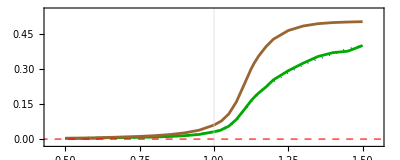

```mathematica
Show[ListPlot[{DatImpR50,DatImpR50k0,DatImpR50k1},Joined->True,Frame->True,PlotRange->{{0.45,1.55},{-0.02,0.55}},PlotStyle->{{Blue,Dotted,AbsoluteThickness[2]},{Darker[Green],Thickness[0.005]},{Brown,Thickness[0.005]}},LabelStyle->{Black,12},PlotLegends->Placed[{"","",""},{0.1,0.65}],GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.1,2.1},PlotStyle->{Red,Thickness[0.002],Dashed}],AspectRatio->0.4]
```

#### (b) Wigner negativity

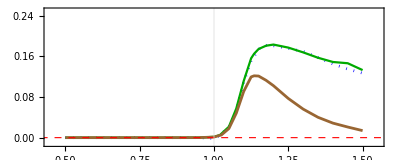

```mathematica
Show[ListPlot[{WminR50,WminR50k0,WminR50k1},Frame->True,Joined->True,PlotRange->{{0.45,1.55},{-0.012,0.25}},PlotStyle->{{Blue,Dotted,AbsoluteThickness[2]},{Darker[Green],Thickness[0.004]},{Brown,Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[0.0,{x,-0.1,2.1},PlotStyle->{Red,Thickness[0.002],Dashed}],AspectRatio->0.4]
```

#### (c) Squeezing distillation

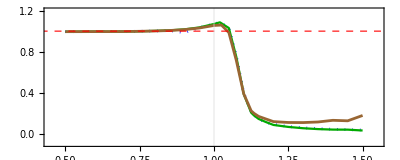

```mathematica
fig2e=Show[ListPlot[{DatSQratioR50,DatSQratioR50k0,DatSQratioR50k1},Joined->True,Frame->True,PlotRange->{{0.45,1.55},{-0.1,1.2}},PlotStyle->{{Blue,Dotted,AbsoluteThickness[2]},{Darker[Green],Thickness[0.004]},{Brown,Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],
Plot[1,{x,-0.1,2.1},PlotStyle->{{Red,Thickness[0.002],Dashed}}],AspectRatio->0.4]
```

#### (d) Displacement sensitivity

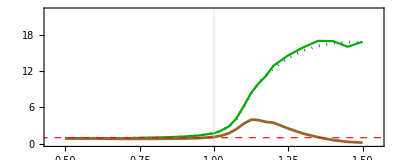

```mathematica
fig2e=Show[ListPlot[{DatCFIdispR50,DatCFIdispR50k0,DatCFIdispR50k1},Joined->True,Frame->True,PlotRange->{{0.45,1.55},{0,22}},PlotStyle->{{Blue,Dotted,AbsoluteThickness[2]},{Darker[Green],Thickness[0.004]},{Brown,Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[{1.0},{x,-0.1,2.1},PlotStyle->{{Red,Thickness[0.002],Dashed},{Darker[Green]}}],AspectRatio->0.4]
```